## Porter’s By Hand Integrals

18

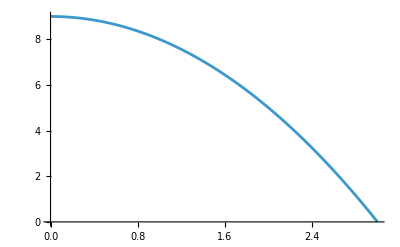

```mathematica
Integrate[9-x^2,{x,0,3}]
Plot[9-x^2,{x,0,3}]
```

```mathematica
Integrate[1/18(9-x^2),{x,0,3}]
```

1

```mathematica
Integrate[1/18(9-x^2),{x,0,1}]
```

13/27

```mathematica
Integrate[1/18(9-x^2),{x,0,2}]
```

23/27

```mathematica
Integrate[1/18(9-x^2),{x,1,2}]
```

10/27

```mathematica
Integrate[1/18(9-x^2),{x,0,x}]
```

x/2-x^3/54

```mathematica
EV=Integrate[x 1/18(9-x^2),{x,0,3}]
```

9/8

```mathematica
Integrate[(x-EV)^2* 1/18(9-x^2),{x,0,3}]
```

171/320

```mathematica
Sqrt[%]//N
```

0.73101

## Quicker using variables

```mathematica
g=9-x^2;
{a,b}={0,3};
A=Integrate[g,{x,a,b}]
k=1/A;
f=k*g
```

18

1/18 (9-x^2)

```mathematica
Integrate[f,{x,a,1}]
Integrate[f,{x,a,2}]
Integrate[f,{x,1,2}]
```

13/27

23/27

10/27

```mathematica
EV=Integrate[x f,{x,a,b}]
Var=Integrate[(x-EV)^2* f,{x,a,b}]
Sqrt[Var]//N
```

9/8

171/320

0.73101

## Use a new function

```mathematica
g=7Exp[-7x];
{a,b}={0,Infinity};
A=Integrate[g,{x,a,b}]
k=1/A;
f=k*g
```

1

7 ⅇ^(-7 x)

```mathematica
Integrate[f,{x,a,1}]//N
Integrate[f,{x,a,2}]//N
Integrate[f,{x,1,2}]//N
```

0.999088

0.999999

0.00091105

```mathematica
EV=Integrate[x f,{x,a,b}]
Var=Integrate[(x-EV)^2* f,{x,a,b}]
Sqrt[Var]
```

1/7

1/49

1/7

## Use The parameter lambda instead of a 7 for The Exponential Distribution (so f3)

```mathematica
$Assumptions=λ>0;
g=λ Exp[-λ x];
{a,b}={0,Infinity};
A=Integrate[g,{x,a,b}]
k=1/A;
f=k*g
```

1

ⅇ^(-x λ) λ

```mathematica
EV=Integrate[x f,{x,a,b}]
Var=Integrate[(x-EV)^2* f,{x,a,b}]
```

1/λ

1/λ^2

## The Normal Distribution (so f1)

```mathematica
$Assumptions = σ>0;
g=1/Sqrt[2*π*σ^2]*Exp[-1/2*((x-μ)/σ)^2]
{a,b}={-Infinity,Infinity};
A=Integrate[g,{x,a,b}]
k=1/A;
f=k*g
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))

1

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))

```mathematica
EV=Integrate[x f,{x,a,b}]
Var=Integrate[(x-EV)^2* f,{x,a,b}]
```

μ

σ^2

## Using Piecewise Defined Functions

This is the help file’s notaton on how to use Piecewise.  You can also just open help (or ask your Robot friend and will encode stuff in Piecewise notation correctly).

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
Piecewise[{{x^2,x<0},{x,x>0}}]
```

Now we repeat what we did at the start of class.

```mathematica
g=Piecewise[{{9-x^2,0<=x<=3},{0,True}}];
{a,b}={-Infinity,Infinity};
A=Integrate[g,{x,a,b}]
k=1/A;
f=k*g
```

18

1/18 (Piecewise[{{9-x^2, 0≤x≤3}, {0, True}}])

```mathematica
Integrate[f,{x,a,1}]
Integrate[f,{x,a,2}]
Integrate[f,{x,1,2}]
```

13/27

23/27

10/27

```mathematica
EV=Integrate[x f,{x,a,b}]
Var=Integrate[(x-EV)^2* f,{x,a,b}]
Sqrt[Var]//N
```

9/8

171/320

0.73101